```mathematica
Quit[]
```

```mathematica
SetDirectory["/Users/saraditsch/Desctop/Wtt/Mathematica"];
```

SetDirectory::cdir: Cannot set current directory to /Users/saraditsch/Desctop/Wtt/Mathematica.

```mathematica
SetDirectory["/scratch/ge84fet/Wtt/Mathematica/MMatrix"];
```

# Tensordecomposition Wtt

## Install Feyncalc

```mathematica
Quiet[Check[Get["FeynCalc`"],Print["FeynCalc is not available."]]]

$FAVerbose=0;
FCCheckVersion[9,3,0];
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

## Define Tensors

### Define variables

```mathematica
epsP5=ChangeDimension[Conjugate[PolarizationVector[p5,μ,Transversality-> True]],D];
SpinorP1=SpinorUD[Momentum[p1,D]];
SpinorP2=SpinorVBarD[Momentum[p2,D]];
SpinorP3=SpinorUBarD[Momentum[p3,D],SMP["m_t"]];
SpinorP4=SpinorVD[Momentum[p4,D],SMP["m_t"]];
Identities={s[1,5] -> 2SMP["m_t"]^2+SMP["m_W"]^2-s[1,2]-s[1,3]-s[1,4], s[2,5]-> 2SMP["m_t"]^2+SMP["m_W"]^2-s[1,2]-s[2,3]-s[2,4], s[3,5]-> 3SMP["m_t"]^2+SMP["m_W"]^2-s[1,3]-s[2,3]-s[3,4], s[4,5]-> 3SMP["m_t"]^2+SMP["m_W"]^2-s[1,4]-s[2,4]-s[3,4]}/.s[3,4]->-(s[2,4]+s[2,3]+s[1,4]+s[1,3]+s[1,2]-4*SMP["m_t"]^2-SMP["m_W"]^2);
AppendTo[Identities,s[3,4]->-(s[2,4]+s[2,3]+s[1,4]+s[1,3]+s[1,2]-4*SMP["m_t"]^2-SMP["m_W"]^2)];
SetMandelstam[s,{p1,p2,p3,p4,p5},{0,0,SMP["m_t"],SMP["m_t"],SMP["m_W"]}];
```

#### Define Tensors in D dimensions

```mathematica
T1=epsP5 FVD[p1,μ] SpinorP2.GSD[p3].SpinorP1 SpinorP3.SpinorP4;
T2=epsP5 FVD[p1,μ] SpinorP2.GSD[p4].SpinorP1 SpinorP3.SpinorP4;
T3=epsP5 FVD[p2,μ] SpinorP2.GSD[p3].SpinorP1 SpinorP3.SpinorP4;
T4=epsP5 FVD[p2,μ] SpinorP2.GSD[p4].SpinorP1 SpinorP3.SpinorP4;
T5=epsP5 FVD[p3,μ] SpinorP2.GSD[p3].SpinorP1 SpinorP3.SpinorP4;
T6=epsP5 FVD[p3,μ] SpinorP2.GSD[p4].SpinorP1 SpinorP3.SpinorP4;

T7=epsP5 FVD[p1,μ] SpinorP2.GSD[p3].SpinorP1 SpinorP3.GSD[p1].SpinorP4;
T8=epsP5 FVD[p1,μ] SpinorP2.GSD[p4].SpinorP1 SpinorP3.GSD[p1].SpinorP4;
T9=epsP5 FVD[p2,μ] SpinorP2.GSD[p3].SpinorP1 SpinorP3.GSD[p1].SpinorP4;
T10=epsP5 FVD[p2,μ] SpinorP2.GSD[p4].SpinorP1 SpinorP3.GSD[p1].SpinorP4;
T11=epsP5 FVD[p3,μ] SpinorP2.GSD[p3].SpinorP1 SpinorP3.GSD[p1].SpinorP4;
T12=epsP5 FVD[p3,μ] SpinorP2.GSD[p4].SpinorP1 SpinorP3.GSD[p1].SpinorP4;
T13=epsP5 FVD[p1,μ] SpinorP2.GSD[p3].SpinorP1 SpinorP3.GSD[p2].SpinorP4;
T14=epsP5 FVD[p1,μ] SpinorP2.GSD[p4].SpinorP1 SpinorP3.GSD[p2].SpinorP4;
T15=epsP5 FVD[p2,μ] SpinorP2.GSD[p3].SpinorP1 SpinorP3.GSD[p2].SpinorP4;
T16=epsP5 FVD[p2,μ] SpinorP2.GSD[p4].SpinorP1 SpinorP3.GSD[p2].SpinorP4;
T17=epsP5 FVD[p3,μ] SpinorP2.GSD[p3].SpinorP1 SpinorP3.GSD[p2].SpinorP4;
T18=epsP5 FVD[p3,μ] SpinorP2.GSD[p4].SpinorP1 SpinorP3.GSD[p2].SpinorP4;

T19=epsP5 FVD[p1,μ] SpinorP2.GSD[p3].SpinorP1 SpinorP3.GSD[p1].GSD[p2].SpinorP4;
T20=epsP5 FVD[p1,μ] SpinorP2.GSD[p4].SpinorP1 SpinorP3.GSD[p1].GSD[p2].SpinorP4;
T21=epsP5 FVD[p2,μ] SpinorP2.GSD[p3].SpinorP1 SpinorP3.GSD[p1].GSD[p2].SpinorP4;
T22=epsP5 FVD[p2,μ] SpinorP2.GSD[p4].SpinorP1 SpinorP3.GSD[p1].GSD[p2].SpinorP4;
T23=epsP5 FVD[p3,μ] SpinorP2.GSD[p3].SpinorP1 SpinorP3.GSD[p1].GSD[p2].SpinorP4;
T24=epsP5 FVD[p3,μ] SpinorP2.GSD[p4].SpinorP1 SpinorP3.GSD[p1].GSD[p2].SpinorP4;
```

#### Contracted Gammas

```mathematica
T25=epsP5 FVD[p1,μ] SpinorP2.GAD[ν].SpinorP1 SpinorP3.GSD[p2].GAD[ν].SpinorP4;
T26=epsP5 FVD[p2,μ] SpinorP2.GAD[ν].SpinorP1 SpinorP3.GSD[p2].GAD[ν].SpinorP4;
T27=epsP5 FVD[p3,μ] SpinorP2.GAD[ν].SpinorP1 SpinorP3.GSD[p2].GAD[ν].SpinorP4;

T28=epsP5 FVD[p1,μ] SpinorP2.GAD[ν].SpinorP1 SpinorP3.GSD[p1].GAD[ν].SpinorP4;
T29=epsP5 FVD[p2,μ] SpinorP2.GAD[ν].SpinorP1 SpinorP3.GSD[p1].GAD[ν].SpinorP4;
T30=epsP5 FVD[p3,μ] SpinorP2.GAD[ν].SpinorP1 SpinorP3.GSD[p1].GAD[ν].SpinorP4;

T31=epsP5 FVD[p1,μ] SpinorP2.GAD[ν].SpinorP1 SpinorP3.GAD[ν].SpinorP4;
T32=epsP5 FVD[p2,μ] SpinorP2.GAD[ν].SpinorP1 SpinorP3.GAD[ν].SpinorP4;
T33=epsP5 FVD[p3,μ] SpinorP2.GAD[ν].SpinorP1 SpinorP3.GAD[ν].SpinorP4;
```

#### All Tensors

```mathematica
Tensors= {T1,T2,T3,T4,T5,T6,T7,T8,T9,T10,T11,T12,T13,T14,T15,T16,T17,T18,T19,T20,T21,T22,T23,T24,T49,T50,T51,T52,T53,T54,T55,T56,T57,T58,T59,T60,T61,T62,T63,T64,T65}//Contract;
```

#### Tensors that give zeros

```mathematica
Tensors={T7,T8,T9,T10,T11,T12,T35,T13,T14,T15,T16,T17,T18,T36,T25,T26,T27,T28,T29,T30}//Contract;
```

#### New Basis

```mathematica
Tensors= {T1,T2,T3,T4,T5,T6,T7,T8,T9,T10,T11,T12,T13,T14,T15,T16,T17,T18,T25,T26,T27,T28,T29,T30}//Contract;
```

```mathematica
TensorsCC = Table[ComplexConjugate[tensor], {tensor, Tensors}];
MMatrixSmall = Table[(FermionSpinSum[DoPolarizationSums[tensorcc*tensor, p5]]//.{D->4}//DiracSimplify)//.Identities//Simplify, {tensor, Tensors}, {tensorcc, TensorsCC}];
Print["Done"]
```

Done

```mathematica
Put[MMatrixSmall, "MMatrix"];
DumpSave["MMatrix.mx",MMatrixSmall];
```

```mathematica
m=Get["/Users/saraditsch/Documents/Wolfram Mathematica/MMatrix"];
```

```mathematica
m=Get["/scratch/ge84fet/Wtt/Mathematica/MMatrix"];
```

```mathematica
RandomKinematics = {s[1, 2] -> RandomPrime[{10000, 10000000}], s[1, 3] -> RandomPrime[{10000, 10000000}], s[1, 4] -> RandomPrime[{10000, 10000000}], s[2, 3] -> RandomPrime[{10000, 10000000}], s[2, 4] -> RandomPrime[{10000, 10000000}], SMP["m_W"] -> RandomPrime[{10000, 10000000}],SMP["m_t"]-> RandomPrime[{10000,10000000}]};
```

```mathematica
MMatrixSmall//.RandomKinematics//Simplify//MatrixRank
```

24

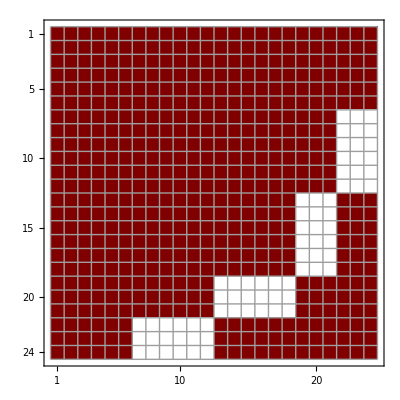

```mathematica
MatrixPlot[MMatrixSmall, Mesh -> All]
```

#### Understand why zeros

```mathematica
S1= SpinorP2.GSD[p3].SpinorP1 SpinorP3.GSD[p1].SpinorP4;
S2= SpinorP2.GAD[ν].SpinorP1 SpinorP3.GSD[p1].GAD[ν].SpinorP4;
```

```mathematica
S1= SpinorP3.GSD[p1].SpinorP4;
S2=  SpinorP3.GSD[p1].GAD[ν].SpinorP4;
```

```mathematica
FermionSpinSum[S1*ComplexConjugate[S2]]//.{D->4}//DiracSimplify
```

4 s(1,2) m_t OverBar[p1]^ν+4 s(2,3) m_t OverBar[p1]^ν-4 s(4,5) m_t OverBar[p1]^ν

```mathematica
S1= SpinorP2.GSD[p3].SpinorP1 ;
S2= SpinorP2.GAD[ν].SpinorP1 ;
```

```mathematica
FermionSpinSum[S1*ComplexConjugate[S2]]//.{D->4}//DiracSimplify
```

0

### Check Linear Independence for Massless Spinors

```mathematica
S1=SpinorP2.GSD[p3].SpinorP1;
S2=SpinorP2.GSD[p4].SpinorP1;
S3=SpinorP2.SpinorP1;
S4=SpinorP2.GSD[p4].GSD[p3].SpinorP1;

Tensors={S1,S2,S3,S4};

TensorsCC= Table[ComplexConjugate[tensor], {tensor, Tensors}];
MMatrixSmall = Table[(FermionSpinSum[DoPolarizationSums[tensorcc*tensor, p5]]//.{D->4}//DiracSimplify)//.Identities//Simplify, {tensor, Tensors}, {tensorcc, TensorsCC}];
MMatrixSmall//.RandomKinematics//Simplify//MatrixRank
```

4

#### Contracted epsilon Not useful

```mathematica
T34=SpinorP2.epsP5.GAD[μ].SpinorP1 SpinorP3.SpinorP4;

T35=SpinorP2.epsP5.GAD[μ].SpinorP1 SpinorP3.GSD[p1].SpinorP4;
T36=SpinorP2.epsP5.GAD[μ].SpinorP1 SpinorP3.GSD[p2].SpinorP4;
T37=SpinorP2.epsP5.GAD[μ].SpinorP1 SpinorP3.GSD[p1].GSD[p2].SpinorP4;

T38=epsP5 SpinorP2.GSD[p3].SpinorP1 SpinorP3.GAD[μ].SpinorP4;
T39=epsP5 SpinorP2.GSD[p4].SpinorP1 SpinorP3.GAD[μ].SpinorP4;
T40=epsP5 SpinorP2.GSD[p3].SpinorP1 SpinorP3.GSD[p1].GAD[μ].SpinorP4;
T41=epsP5 SpinorP2.GSD[p4].SpinorP1 SpinorP3.GSD[p2].GAD[μ].SpinorP4;
```

#### Define Symmetrised Tensors Not useful!!!

```mathematica
T25=epsP5 FVD[p1+p2,μ] SpinorP2.GSD[p3+p4].SpinorP1 SpinorP3.SpinorP4;
T26=epsP5 FVD[p1+p2,μ] SpinorP2.GSD[p3-p4].SpinorP1 SpinorP3.SpinorP4;
T27=epsP5 FVD[p1-p2,μ] SpinorP2.GSD[p3+p4].SpinorP1 SpinorP3.SpinorP4;
T28=epsP5 FVD[p1-p2,μ] SpinorP2.GSD[p3-p4].SpinorP1 SpinorP3.SpinorP4;
T29=epsP5 FVD[p3,μ] SpinorP2.GSD[p3+p4].SpinorP1 SpinorP3.SpinorP4;
T30=epsP5 FVD[p3,μ] SpinorP2.GSD[p3-p4].SpinorP1 SpinorP3.SpinorP4;

T31=epsP5 FVD[p1+p2,μ] SpinorP2.GSD[p3+p4].SpinorP1 SpinorP3.GSD[p1+p2].SpinorP4;
T32=epsP5 FVD[p1+p2,μ] SpinorP2.GSD[p3+p4].SpinorP1 SpinorP3.GSD[p1-p2].SpinorP4;
T33=epsP5 FVD[p1-p2,μ] SpinorP2.GSD[p3+p4].SpinorP1 SpinorP3.GSD[p1+p2].SpinorP4;
T34=epsP5 FVD[p1-p2,μ] SpinorP2.GSD[p3+p4].SpinorP1 SpinorP3.GSD[p1-p2].SpinorP4;
T35=epsP5 FVD[p3,μ] SpinorP2.GSD[p3+p4].SpinorP1 SpinorP3.GSD[p1+p2].SpinorP4;
T36=epsP5 FVD[p3,μ] SpinorP2.GSD[p3+p4].SpinorP1 SpinorP3.GSD[p1-p2].SpinorP4;
T37=epsP5 FVD[p1+p2,μ] SpinorP2.GSD[p3-p4].SpinorP1 SpinorP3.GSD[p1+p2].SpinorP4;
T38=epsP5 FVD[p1+p2,μ] SpinorP2.GSD[p3-p4].SpinorP1 SpinorP3.GSD[p1-p2].SpinorP4;
T39=epsP5 FVD[p1-p2,μ] SpinorP2.GSD[p3-p4].SpinorP1 SpinorP3.GSD[p1+p2].SpinorP4;
T40=epsP5 FVD[p1-p2,μ] SpinorP2.GSD[p3-p4].SpinorP1 SpinorP3.GSD[p1-p2].SpinorP4;
T41=epsP5 FVD[p3,μ] SpinorP2.GSD[p3-p4].SpinorP1 SpinorP3.GSD[p1+p2].SpinorP4;
T42=epsP5 FVD[p3,μ] SpinorP2.GSD[p3-p4].SpinorP1 SpinorP3.GSD[p1-p2].SpinorP4;

T43=epsP5 FVD[p1+p2,μ] SpinorP2.GSD[p3+p4].SpinorP1 SpinorP3.GSD[p1].GSD[p2].SpinorP4;
T44=epsP5 FVD[p1+p2,μ] SpinorP2.GSD[p3-p4].SpinorP1 SpinorP3.GSD[p1].GSD[p2].SpinorP4;
T45=epsP5 FVD[p1-p2,μ] SpinorP2.GSD[p3+p4].SpinorP1 SpinorP3.GSD[p1].GSD[p2].SpinorP4;
T46=epsP5 FVD[p1-p2,μ] SpinorP2.GSD[p3-p4].SpinorP1 SpinorP3.GSD[p1].GSD[p2].SpinorP4;
T47=epsP5 FVD[p3,μ] SpinorP2.GSD[p3+p4].SpinorP1 SpinorP3.GSD[p1].GSD[p2].SpinorP4;
T48=epsP5 FVD[p3,μ] SpinorP2.GSD[p3-p4].SpinorP1 SpinorP3.GSD[p1].GSD[p2].SpinorP4;
```

#### Compare with Form

```mathematica
FormToMathematicaLanguage={s12->s[1,2],s13->s[1,3],s14->s[1,4],s23->s[2,3],s24->s[2,4],mt->SMP["m_t"],mw->SMP["m_W"]};
```

```mathematica
Form=Import["/Users/saraditsch/Desktop/Wtt/Form_ttW/M_Matrix_Form.txt"];
Form1=StringSplit[Form,";"];
Form2=Form1[[1;;576]];
Form3=ArrayReshape[Form2,{24,24}];
Form4=Table[StringDelete[Form3[[i]],"\n"|"\r"],{i,24}];
MMatrixForm=ToExpression[Form4]//.FormToMathematicaLanguage;
```

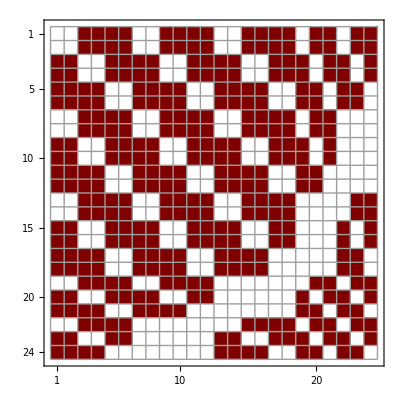

```mathematica
MatrixPlot[(MMatrixForm-MMatrixSmall)//Together//Simplify,Mesh->All]
```

```mathematica
MMatrixForm[[1,3]]//Simplify
```

1/m_W^2(s(1,2)+s(1,3)+s(1,4)-2 m_t^2) (s(1,2)+s(2,3)+s(2,4)-2 m_t^2) ((s(1,2)+s(1,3)+s(2,3)) m_t^2-s(1,3) s(2,3)-m_t^4) (s(1,2)+s(1,3)+s(1,4)+s(2,3)+s(2,4)-m_W^2)

```mathematica
MMatrixSmall[[1,3]]//Simplify
```

1/m_W^2((s(1,2)+s(1,3)+s(2,3)) m_t^2-s(1,3) s(2,3)-m_t^4) (4 m_t^4 (s(1,2)+s(1,3)+s(1,4)+s(2,3)+s(2,4)-m_W^2)-2 (2 s(1,2)+s(1,3)+s(1,4)+s(2,3)+s(2,4)) m_t^2 (s(1,2)+s(1,3)+s(1,4)+s(2,3)+s(2,4)-m_W^2)+2 s(1,2) m_W^4-(3 (s(1,2))^2+3 (s(1,3)+s(1,4)+s(2,3)+s(2,4)) s(1,2)+(s(1,3)+s(1,4)) (s(2,3)+s(2,4))) m_W^2+(s(1,2)+s(1,3)+s(1,4)) (s(1,2)+s(2,3)+s(2,4)) (s(1,2)+s(1,3)+s(1,4)+s(2,3)+s(2,4)))

```mathematica
ComplexConjugate[T1//Contract]*T3//Contract//FermionSpinSum//DiracSimplify
```

-16 s(2,3) m_t^4 (p1·ε(p5)) (p2·ε^*(p5))+16 s(4,5) m_t^4 (p1·ε(p5)) (p2·ε^*(p5))+16 (s(2,3))^2 m_t^2 (p1·ε(p5)) (p2·ε^*(p5))+16 s(1,2) s(2,3) m_t^2 (p1·ε(p5)) (p2·ε^*(p5))+4 s(2,3) s(3,4) m_t^2 (p1·ε(p5)) (p2·ε^*(p5))-16 s(2,3) s(4,5) m_t^2 (p1·ε(p5)) (p2·ε^*(p5))-4 s(3,4) s(4,5) m_t^2 (p1·ε(p5)) (p2·ε^*(p5))-4 (s(2,3))^2 s(3,4) (p1·ε(p5)) (p2·ε^*(p5))-4 s(1,2) s(2,3) s(3,4) (p1·ε(p5)) (p2·ε^*(p5))+4 s(2,3) s(3,4) s(4,5) (p1·ε(p5)) (p2·ε^*(p5))

```mathematica
p1
```